#### Factorial function

In this notebook, we will study the factorial function. We see how to use Mathematica to compute and use the functions defined in clasess... and so on ...

```mathematica
Factorial[3]
```

6

Alternatively

```mathematica
3!
```

6

```mathematica
(1/2)!
```

(√π)/2

```mathematica
N[(-1/4)!]
```

1.22542

```mathematica
Table[n!,{n,-2,5}]
```

{ComplexInfinity,ComplexInfinity,1,1,2,6,24,120}

```mathematica
Table[n,{n,-2,5}]!
```

{ComplexInfinity,ComplexInfinity,1,1,2,6,24,120}

Plot factorial:

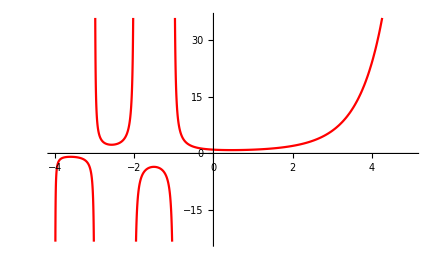

```mathematica
Plot[n!,{n,-4,5},PlotStyle->Red]
```

Evaluate for complex arguments (it was not studied in classes):

```mathematica
N[(2+3*I)!]
```

-0.440113-0.0636372 ⅈ

Plot of the absolute value of Factorial in the complex plane:

```mathematica
Plot3D[Abs[Factorial[x+I y]],{x,-5,2},{y,-1,1}]
```

-Graphics3D-

#### Gamma Function

Using is the Euler gamma function Γ(z)

```mathematica
Gamma[3]
```

2

```mathematica
Factorial[3]
```

6

```mathematica
3!
```

6

```mathematica
Gamma[1/2]
```

√π

Of course Γ[z+1]=z! see the next table

```mathematica
Table[Gamma[n+1],{n,1,5}]
Table[(n)!,{n,1,5}]
```

{1,2,6,24,120}

{1,2,6,24,120}

#### Double factorial of n

```mathematica
0!!
```

1

```mathematica
1!!
```

1

```mathematica
(-1)!!
```

1

```mathematica
(-3)!!
```

-1

```mathematica
Table[n!!,{n,10}]
```

{1,2,3,8,15,48,105,384,945,3840}

Note the numerical evaluation

```mathematica
(1.2)!!
```

1.10414

```mathematica
N[(1/4)!]
```

0.906402

Plot double factorial:

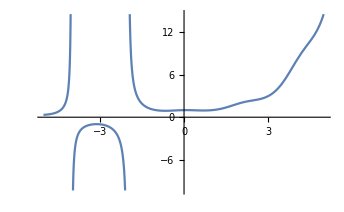

```mathematica
Plot[n!!,{n,-5,5}]
```

```mathematica
Plot3D[Abs[Factorial2[x+I y]],{x,-5,2},{y,-1,1}]
```

-Graphics3D-

#### Beta function

For example : let see the next integral

```mathematica
∫_0^(π/2) √Tan[x] ⅆx
N[∫_0^(π/2) √Tan[x] ⅆx]
```

π/(√2)

2.22144

Now, using the beta function

```mathematica
N[0.5*Beta[3/4,1/4]]
```

2.22144

```mathematica
∫√Tan[x] ⅆx
```

1/(2 √2)(-2 ArcTan[1-√2 √Tan[x]]+2 ArcTan[1+√2 √Tan[x]]+Log[1-√2 √Tan[x]+Tan[x]]-Log[1+√2 √Tan[x]+Tan[x]])

```mathematica
N[∫_0^(π/2) √Cos[x] ⅆx]
```

1.19814

```mathematica
∫_0^(π/2) Cos[x]^2*Sin[x]^2 ⅆx
```

π/16

```mathematica
(1/2)*Beta[3/2,3/2]
```

π/16

Quiz 3

```mathematica
∫_0^(π/2) Cos[x]^4*Sin[x]^4 ⅆx
```

(3 π)/256

#### Error Function

```mathematica
∫ⅇ^(-x^2)ⅆx
```

1/2 √π Erf[x]

```mathematica
∫_0^∞ ⅇ^(-x^2)ⅆx
```

(√π)/2